Stabilizer Formalism

Stabilizers: Conceptpaclet:Q3/tutorial/StabilizerFormalism#1514564784 | Properties of Stabilizerspaclet:Q3/tutorial/StabilizerFormalism#1536912246
Stabilizer Formalism: Overviewpaclet:Q3/tutorial/StabilizerFormalism#1424127932 | Stabilizer Circuitspaclet:Q3/tutorial/StabilizerFormalism#90183241
The Pauli and Clifford Groupspaclet:Q3/tutorial/StabilizerFormalism#1626285955 | Examplespaclet:Q3/tutorial/StabilizerFormalism#785401655

See also Section 6.3 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

Stabilizer formalism is a mathematical framework that describes and characterizes states on multiple qubits in a compact way in terms of operators preserving the states. It provides a powerful and elegant tool to construct quantum error-correction codes, to build and analyse various quantum algorithms, and to examine the properties of the graph states and one-way quantum computation, and to formulate topological quantum computation.

Stabilizer formalism was first put forward by Gottesman (1996). This formalism is explained in great detail in Gottesman (1997) and is also presented in Nielsen & Chuang (2011) and the Quantum Workbookhttps://doi.org/10.1007/978-3-030-91214-7. Recently, stabilizer formalism has been extended to the measurement-based quantum computation scheme (Browne & Briegel, 2016https://doi.org/10.1002/9783527805785.ch21).

FullPauliGrouppaclet:Q3/ref/FullPauliGroupQ3 Package Symbol | The group of tensor products of single-qubit Pauli operators.
PauliGrouppaclet:Q3/ref/PauliGroupQ3 Package Symbol | The group of tensor products of single-qubit Pauli operators ignoring global phase factors.
FullCliffordGrouppaclet:Q3/ref/FullCliffordGroupQ3 Package Symbol | The normalizer of the full Pauli group.
CliffordGrouppaclet:Q3/ref/CliffordGroupQ3 Package Symbol | The noramlizer of the full Pauli group ignoring global phase factors.
GottesmanVectorpaclet:Q3/ref/GottesmanVectorQ3 Package Symbol | The binary vector corresponding to a Pauli operator. 
FromGottesmanVectorpaclet:Q3/ref/FromGottesmanVectorQ3 Package Symbol | The Pauli operator correspoinding to a Gottesman vector.
GottesmanMatrixpaclet:Q3/ref/GottesmanMatrixQ3 Package Symbol | The binary symplectic matrix corresponding to a Clifford group.
FromGottesmanMatrixpaclet:Q3/ref/FromGottesmanMatrixQ3 Package Symbol | The Clifford operator corresponding to a Gottesman matrix.
Stabilizerpaclet:Q3/ref/StabilizerQ3 Package Symbol | Returns the stabilizer subgroup of a given state.

Functions useful to study stabilizer formalism.

Make sure that the Q3 package is loaded to use the demonstrations in this document.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Stabilizers: Concept

Let 𝒢 be a group of operators acting on the quantum states of a quantum system. In quantum computation, the most relevant group is the unitary group 𝒰(2^n) of quantum logic gate operators on n qubits.

### Stabilizer of a quantum state

Suppose that |ψ⟩ is a quantum state. When it remains unchanged under an operator G in the group 𝒢, Gψ=ψ, the state is said to be stabilized by G, or equivalently, G is said to stabilize ψ.

For example, Bell state Φ=(00+11)/√2is stabilized by X⊗X.

Construct a Bell state.

```mathematica
in=BellState[S@{1,2},0]
```

(0_(,,S_(,,1))0_(,,S_(,,2))+1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)

Consider an operator stabilizing the above state.

```mathematica
op=S[1,1]**S[2,1]
op//PauliForm
```

S_(,,1)^(,,X)S_(,,2)^(,,X)

X⊗X

Act the operator on the input state to see the resulting state be the same.

```mathematica
out=op**in
```

(0_(,,S_(,,1))0_(,,S_(,,2)))/(√2)+(1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)

Moreover, the set of operators that stabilize a quantum state ψ forms a subgroup of G. This subgroup is called the stabilizer subgroup or simply stabilizer of the quantum state ψ.

For example, the above Bell state Φ is also stabilized by Z⊗Z and -Y⊗Y as well. These operators form a subgroup,  𝒮:={I⊗I,X⊗X,Z⊗Z,-Y⊗Y}, of 𝒰(4). In other words, the subgroup 𝒮 is the stabilizer of Bell state Φ.

Consider again the input state as before.

```mathematica
in=(Ket[S@{1,2}->0]+Ket[S@{1,2}->1])/Sqrt[2]
```

(0_(,,S_(,,1))0_(,,S_(,,2))+1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)

These are the whole stabilizing subgroup of the above state.

```mathematica
grp={1, S[1,1]**S[2,1],S[1,3]**S[2,3],-S[1,2]**S[2,2]};
PauliForm[grp]
```

{I⊗I,X⊗X,Z⊗Z,-(Y⊗Y)}

Check that every element gives the same state as the input state.

```mathematica
new=grp**in
```

{(0_(,,S_(,,1))0_(,,S_(,,2)))/(√2)+(1_(,,S_(,,1))1_(,,S_(,,2)))/(√2),(0_(,,S_(,,1))0_(,,S_(,,2)))/(√2)+(1_(,,S_(,,1))1_(,,S_(,,2)))/(√2),(0_(,,S_(,,1))0_(,,S_(,,2)))/(√2)+(1_(,,S_(,,1))1_(,,S_(,,2)))/(√2),(0_(,,S_(,,1))0_(,,S_(,,2)))/(√2)+(1_(,,S_(,,1))1_(,,S_(,,2)))/(√2)}

### Stabilizer of a subspace

The notion of stabilizer is extended to subspaces. Let 𝒱 be a subspace of the Hilbert space associated with a quantum system. The stabilizer 𝒮 of 𝒱 is the set of all operators G in 𝒢 that stabilize all quantum states in 𝒱.

For example, consider the code space 𝒱 of the bit- flip correction code. 𝒱 is spanned by the two logical basis states | 000 ⟩ and | 111 ⟩. The stabilizer 𝒮 of 𝒱 is given by 𝒮:={I⊗I⊗I,Z⊗Z⊗I,I⊗Z⊗Z,Z⊗I⊗Z}.

Consider a subspace 𝒱 spanned by this basis.

```mathematica
ss=S[{1,2,3},$];
bs={Ket[ss->0],Ket[S@{1,2,3}->1]}
```

{0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)),1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))}

The stabilizer 𝒮 of 𝒱 is given as follows.

```mathematica
grp={1,S[1,3]**S[2,3],S[2,3]**S[3,3],S[1,3]**S[3,3]};
grp//PauliForm
```

{I⊗I⊗I,Z⊗Z⊗I,I⊗Z⊗Z,Z⊗I⊗Z}

Check that the above group indeed stabilizes 𝒱.

```mathematica
grp**bs[[1]]
grp**bs[[2]]
```

{0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)),0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)),0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3)),0_(,,S_(,,1))0_(,,S_(,,2))0_(,,S_(,,3))}

-Graphics-

As another example, consider the code space of the phase-flip correction code. It is spanned by the following two logical basis states.

```mathematica
ss=S[{1,2,3},$];
bs={ProductState[ss->{1,1}/Sqrt[2]],ProductState[ss->{1,-1}/Sqrt[2]]}
```

{((,,0)/(√2)+(,,1)/(√2))_(S_(,,1))⊗((,,0)/(√2)+(,,1)/(√2))_(S_(,,2))⊗((,,0)/(√2)+(,,1)/(√2))_(S_(,,3)),((,,0)/(√2)-(,,1)/(√2))_(S_(,,1))⊗((,,0)/(√2)-(,,1)/(√2))_(S_(,,2))⊗((,,0)/(√2)-(,,1)/(√2))_(S_(,,3))}

The stabilizer 𝒮 of 𝒱 is given as follows.

```mathematica
grp={1,S[1,1]**S[2,1],S[2,1]**S[3,1],S[1,1]**S[3,1]};
grp//PauliForm
```

{I⊗I⊗I,X⊗X⊗I,I⊗X⊗X,X⊗I⊗X}

Check that the above group indeed stabilizes 𝒱.

```mathematica
grp**bs[[1]]//Elaborate//KetFactor
```

-Graphics-

```mathematica
grp**bs[[2]]//Elaborate//KetFactor
```

-Graphics-

Stabilizer Formalism: Overview

A quantum error-correction code encodes quantum states of a fixed number of qubits in a subspace of the Hilbert space of more qubits. This subspace is called the code space of the particular code. The code space is specified by the logical basis states (called codewords) spanning it.

A natural way to analyze the code is to inspect how the quantum states in the code space are affected by the errors. Mathematically, this is achieved by examining the evolution of the quantum states under the quantum operation describing the error process. This corresponds to the usual Schrödinger picture of dynamical processes in quantum mechanics.

It may sound odd at first glance, but a code space can also be specified by operators that preserve it, and that is the goal of stabilizer formalism. In a broad sense, it is analogous to the Heisenberg picture of dynamical processes in quantum mechanics.

To get an idea about the tasks to be established in stabilizer formalism, it is convenient to examine the effects of extreme classes of general quantum operations, unitary gates and measurements.

### Unitary Gates

Consider a unitary operation U on a quantum system, and suppose that 𝒮 stabilizes a given subspace 𝒱. The unitary operation U transforms 𝒱 onto U 𝒱 U^†, and in general, 𝒮 does not stabilizes the new subspace any longer. Then, what is the stabilizer of the new subspace U 𝒱 U^†?

Suppose that an operator G is an element of the stabilizer 𝒮. Then, Gψ=ψ for any quantum state ψ in the subspace 𝒱. We observe that U G U^†Uψ=Uψ. This means that U G U^† stabilizes Uψ, and hence the whole subspace U 𝒱. In other words, the group U 𝒮 U^† is the stabilizer of the new subspace U 𝒱. Now, suppose that {G_j} is a generating set of stabilizer 𝒮. Since any element of 𝒮 is generated by G_j, any operator of the form U G U^† for G∈𝒮 is generated by U G_j U^†. That is, the new stabilizer U 𝒮 U^† is generated by U G_j U^†. To sum up, under a unitary operation U, the generators G_j of the stabilizer are transformed as G_j↦U G_j U^†.

As the unitary operation U changes logical basis states, the logical Pauli operators must accordingly transform. Following the above line of arguments for the generators of the stabilizer, we see that the logical Pauli operators also transform in the same manner, X_j↦U X_j U^† and Z_j↦U Z_j U^†.

### Measurements

Consider an observable M on a quantum system, and suppose that 𝒮 stabilizes a given subspace 𝒱. After the measurement of M, subspace 𝒱 is projected onto onto P_m 𝒱, where P_m is the projection onto the eigenspace belonging to eigenvalue m of M.

Now, we ask a similar question as in the above, that is, what is the stabilizer of the new subspace P_m 𝒱? Unlike the case of unitary gates, it is in general highly nontrivial to find the stabilizer of the new subspace not to speak of expressing the new generators in terms of original generators. Finding new logical Pauli operators associated with the new subspace is also tedious because without establishing an explicit relation between the new and initial stabilizer, one has to find the local operators from the scratch.

### Benefits from Restriction

So far, the discussion has been completely general. However, for many quantum information processing procedures including quantum error correction, the Pauli operators and their tensor products are sufficient. Therefore, it would be useful to focus on unitary operators  the conjugation by which transforms the tensor products of single-qubit Pauli operators to such products. In this case, stabilizer formalism turns out to be extremely simple and insightful.

As a matter fact, in this case, describing quantum operations by tracking the stabilizer is far more (i.e., exponentially) efficient than tracking the subspace or quantum states. This is why stabilizer formalism is so powerful.

The Pauli and Clifford Groups

In general, finding the stabilizer of a given subspace and vice versa may be non-trivial. Fortunately, when operators are restricted to the Pauli operators or their tensor products on a fixed number n of qubits, the stabilizers have particularly simple structures and useful properties. Moreover, in accordance with the discretization of errors, such operators are enough to describe any quantum noise operation. Therefore, it is useful to restrict the parent group of any stabilizer to the Pauli group. This naturally restricts the allowed unitary transformations to the Clifford group as well.

The Pauli group is the group of all tensor products of single-qubit Pauli operators. The elements of the Pauli group are called (multi-qubit) Pauli operators. The Clifford group is the group of all unitary operators that keep the Pauli group invariant (that is, map a Pauli operator to another Pauli operator) under conjugation. The elements of the Clifford group are called Clifford operators.

Properties of the Pauli and Clifford groups are explained in detail in another document, the Pauli and Clifford Groups. Here we summarises some properties directly related to stabilizer formalism.

### The Pauli Group

The full Pauli group 𝒫̃(n) on n qubits consists of tensor products of single-qubit Pauli operators I, X, Y, and Z associated with the 2×2 matrices

I=(1 | 0
0 | 1), X=(0 | 1
1 | 0), Y=(0 | -ⅈ
ⅈ | 0), Z=(1 | 0
0 | -1).

Enlisting the elements, it is given by

𝒫̃(n)={±1,±ⅈ}×{I,X,Y,Z}^(⊗n).

The additional phase factors ±1 and ±ⅈ are required because the product of two Pauli operators gives another Pauli operator accompanied by factor ±ⅈ. Otherwise, the underlying set is not closed under the group multiplication.

Elements of the full Pauli group are called (multi-qubit) Pauli operators (or Pauli strings).

```mathematica
grp=FullPauliGroup[S@{1,2}]
elm=GroupElements[grp];
elm//PauliForm
```

FullPauliGroup[{S_(,,1),S_(,,2)}]

{I⊗I,X⊗I,Z⊗I,Y⊗I,I⊗X,X⊗X,Z⊗X,Y⊗X,I⊗Z,X⊗Z,Z⊗Z,Y⊗Z,I⊗Y,X⊗Y,Z⊗Y,Y⊗Y,-(I⊗I),-(X⊗I),-(Z⊗I),-(Y⊗I),-(I⊗X),-(X⊗X),-(Z⊗X),-(Y⊗X),-(I⊗Z),-(X⊗Z),-(Z⊗Z),-(Y⊗Z),-(I⊗Y),-(X⊗Y),-(Z⊗Y),-(Y⊗Y),ⅈ I⊗I,ⅈ X⊗I,ⅈ Z⊗I,ⅈ Y⊗I,ⅈ I⊗X,ⅈ X⊗X,ⅈ Z⊗X,ⅈ Y⊗X,ⅈ I⊗Z,ⅈ X⊗Z,ⅈ Z⊗Z,ⅈ Y⊗Z,ⅈ I⊗Y,ⅈ X⊗Y,ⅈ Z⊗Y,ⅈ Y⊗Y,-ⅈ I⊗I,-ⅈ X⊗I,-ⅈ Z⊗I,-ⅈ Y⊗I,-ⅈ I⊗X,-ⅈ X⊗X,-ⅈ Z⊗X,-ⅈ Y⊗X,-ⅈ I⊗Z,-ⅈ X⊗Z,-ⅈ Z⊗Z,-ⅈ Y⊗Z,-ⅈ I⊗Y,-ⅈ X⊗Y,-ⅈ Z⊗Y,-ⅈ Y⊗Y}

Count the elements in the two-qubit Pauli group.

```mathematica
GroupOrder[grp]
```

64

The number of elements quickly increases with the number of qubits, and it is more convenient to describe the full Pauli group in terms of generators. The Pauli group on n qubits is generated by tensor products of the Pauli operators acting non-trivially on one and only one qubit.

For example, the full Pauli group on two qubits are generated by single-qubit Pauli operators.

```mathematica
gnr=GroupGenerators[grp];
PauliForm[gnr]
```

{X⊗I,Y⊗I,Z⊗I,I⊗X,I⊗Y,I⊗Z}

Pauli operators (i.e., elements in the full Pauli group) have two extremely useful properties that eventually determine the group-theoretical structure of the stabilizers and stabilizer codes.

Any two elements of the full Pauli group either commute or anti-commute with each
other. The rule is also simple that allows to determine which elements commute and which elements anti-commute.

Every element of the Pauli group squares to ±I. The elements that square to I have eigenvalues ±1 whereas those that square to −I have eigenvalues ±ⅈ.

For example, consider two-qubit Pauli operators.

```mathematica
EchoTiming[mat=Outer[GottesmanTest,elm,elm];]
TableForm[mat,TableHeadings->{PauliForm@elm,PauliForm@elm},TableAlignments->Right]
```

2.73536

| I⊗I | X⊗I | Z⊗I | Y⊗I | I⊗X | X⊗X | Z⊗X | Y⊗X | I⊗Z | X⊗Z | Z⊗Z | Y⊗Z | I⊗Y | X⊗Y | Z⊗Y | Y⊗Y | -(I⊗I) | -(X⊗I) | -(Z⊗I) | -(Y⊗I) | -(I⊗X) | -(X⊗X) | -(Z⊗X) | -(Y⊗X) | -(I⊗Z) | -(X⊗Z) | -(Z⊗Z) | -(Y⊗Z) | -(I⊗Y) | -(X⊗Y) | -(Z⊗Y) | -(Y⊗Y) | ⅈ I⊗I | ⅈ X⊗I | ⅈ Z⊗I | ⅈ Y⊗I | ⅈ I⊗X | ⅈ X⊗X | ⅈ Z⊗X | ⅈ Y⊗X | ⅈ I⊗Z | ⅈ X⊗Z | ⅈ Z⊗Z | ⅈ Y⊗Z | ⅈ I⊗Y | ⅈ X⊗Y | ⅈ Z⊗Y | ⅈ Y⊗Y | -ⅈ I⊗I | -ⅈ X⊗I | -ⅈ Z⊗I | -ⅈ Y⊗I | -ⅈ I⊗X | -ⅈ X⊗X | -ⅈ Z⊗X | -ⅈ Y⊗X | -ⅈ I⊗Z | -ⅈ X⊗Z | -ⅈ Z⊗Z | -ⅈ Y⊗Z | -ⅈ I⊗Y | -ⅈ X⊗Y | -ⅈ Z⊗Y | -ⅈ Y⊗Y
I⊗I | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
X⊗I | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
Z⊗I | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
Y⊗I | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
I⊗X | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
X⊗X | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1
Z⊗X | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
Y⊗X | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1
I⊗Z | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
X⊗Z | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
Z⊗Z | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
Y⊗Z | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
I⊗Y | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1
X⊗Y | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1
Z⊗Y | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1
Y⊗Y | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1
-(I⊗I) | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
-(X⊗I) | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
-(Z⊗I) | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
-(Y⊗I) | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
-(I⊗X) | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-(X⊗X) | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1
-(Z⊗X) | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
-(Y⊗X) | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1
-(I⊗Z) | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
-(X⊗Z) | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
-(Z⊗Z) | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
-(Y⊗Z) | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
-(I⊗Y) | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1
-(X⊗Y) | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1
-(Z⊗Y) | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1
-(Y⊗Y) | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1
ⅈ I⊗I | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
ⅈ X⊗I | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
ⅈ Z⊗I | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
ⅈ Y⊗I | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
ⅈ I⊗X | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
ⅈ X⊗X | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1
ⅈ Z⊗X | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
ⅈ Y⊗X | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1
ⅈ I⊗Z | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
ⅈ X⊗Z | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
ⅈ Z⊗Z | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
ⅈ Y⊗Z | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
ⅈ I⊗Y | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1
ⅈ X⊗Y | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1
ⅈ Z⊗Y | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1
ⅈ Y⊗Y | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1
-ⅈ I⊗I | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
-ⅈ X⊗I | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
-ⅈ Z⊗I | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
-ⅈ Y⊗I | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
-ⅈ I⊗X | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
-ⅈ X⊗X | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1
-ⅈ Z⊗X | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
-ⅈ Y⊗X | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1
-ⅈ I⊗Z | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
-ⅈ X⊗Z | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
-ⅈ Z⊗Z | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
-ⅈ Y⊗Z | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
-ⅈ I⊗Y | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1
-ⅈ X⊗Y | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1
-ⅈ Z⊗Y | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1
-ⅈ Y⊗Y | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1

```mathematica
sqr=elm**elm;
Thread[PauliForm[elm]->sqr]//TableForm
```

I⊗I→1
X⊗I→1
Z⊗I→1
Y⊗I→1
I⊗X→1
X⊗X→1
Z⊗X→1
Y⊗X→1
I⊗Z→1
X⊗Z→1
Z⊗Z→1
Y⊗Z→1
I⊗Y→1
X⊗Y→1
Z⊗Y→1
Y⊗Y→1
-(I⊗I)→1
-(X⊗I)→1
-(Z⊗I)→1
-(Y⊗I)→1
-(I⊗X)→1
-(X⊗X)→1
-(Z⊗X)→1
-(Y⊗X)→1
-(I⊗Z)→1
-(X⊗Z)→1
-(Z⊗Z)→1
-(Y⊗Z)→1
-(I⊗Y)→1
-(X⊗Y)→1
-(Z⊗Y)→1
-(Y⊗Y)→1
ⅈ I⊗I→-1
ⅈ X⊗I→-1
ⅈ Z⊗I→-1
ⅈ Y⊗I→-1
ⅈ I⊗X→-1
ⅈ X⊗X→-1
ⅈ Z⊗X→-1
ⅈ Y⊗X→-1
ⅈ I⊗Z→-1
ⅈ X⊗Z→-1
ⅈ Z⊗Z→-1
ⅈ Y⊗Z→-1
ⅈ I⊗Y→-1
ⅈ X⊗Y→-1
ⅈ Z⊗Y→-1
ⅈ Y⊗Y→-1
-ⅈ I⊗I→-1
-ⅈ X⊗I→-1
-ⅈ Z⊗I→-1
-ⅈ Y⊗I→-1
-ⅈ I⊗X→-1
-ⅈ X⊗X→-1
-ⅈ Z⊗X→-1
-ⅈ Y⊗X→-1
-ⅈ I⊗Z→-1
-ⅈ X⊗Z→-1
-ⅈ Z⊗Z→-1
-ⅈ Y⊗Z→-1
-ⅈ I⊗Y→-1
-ⅈ X⊗Y→-1
-ⅈ Z⊗Y→-1
-ⅈ Y⊗Y→-1

In most applications of Pauli operators, an explicit multiplication table is not necessary, commutation (or anti-commutation) of the elements is sufficient. As long as the commutation of the elements is concerned, one can ignore the phase factors ±1 and ±ⅈ in the elements of the full Pauli group. Mathematically, this can be achieved by considering the quotient group

𝒫(n):=𝒫̃(n)/𝒵(n)

where 𝒵(n):={±I^(⊗n), ±ⅈ I^(⊗n)} is the center (the largest Abelian invariant subgroup) of 𝒫̃(n).  This quotient group is called the Pauli group.

As a quotient group, the Pauli group is a group of cosets, and the elements of the same meaning belong to the same coset.

In Q3, cosets in the Pauli group are denoted by their representatives.

```mathematica
grp=PauliGroup[S@{1,2}]
```

PauliGroup[{S_1,S_2}]

```mathematica
GroupOrder[grp]
```

16

```mathematica
elm=GroupElements[grp];
elm//PauliForm
```

{I⊗I,X⊗I,Z⊗I,Y⊗I,I⊗X,X⊗X,Z⊗X,Y⊗X,I⊗Z,X⊗Z,Z⊗Z,Y⊗Z,I⊗Y,X⊗Y,Z⊗Y,Y⊗Y}

```mathematica
gnr=GroupGenerators[grp];
gnr//PauliForm
```

{X⊗I,Y⊗I,Z⊗I,I⊗X,I⊗Y,I⊗Z}

### Gottesman Vectors

Ignoring the phase factors leads to a drastically simple structure of 𝒫(n), compared to the full Pauli group  𝒫̃(n). For example, X Y is now equal to Y X, that is, (X𝒵)(Y𝒵)=(X Y)𝒵=(Y X)𝒵. This means that unlike the full Pauli group  𝒫̃(n), the Pauli group  𝒫(n) is Abelian.

Moreover, since X Z=Z X=Y in the Pauli group 𝒫(n), the latter is isomorphic to ℤ_2^(2n) with group multiplication given by addition modulo 2. By inspection, it is clear that the following correspondence yields an isomorphism between 𝒫(n) and ℤ_2^(2n):

X<->(1,0), Z<->(0,1)

The correspondence Y<->(1,1) follows automatically from the group multiplication (between cosets).

Equivalently, a Pauli operator of the form

P=X^x_1 Z^z_1⊗X^x_2Z^z_2⊗…⊗X^x_n Z^z_n∈𝒫(n)

corresponds to the vector

v=(x_1,z_1,x_2,z_2,…,…,x_n,z_n)∈ℤ_2^(2n).

As another example, consider the following three-qubit Pauli operator.

```mathematica
op=S[1,1]**S[2,3]**S[3,2];
op//PauliForm
```

X⊗Z⊗Y

Get the Gottesman vector corresponding to op.

```mathematica
vec=GottesmanVector[op,S@{1,2,3}]
```

{1,0,0,1,1,1}

Here is an exhaustive conversion table of the whole Pauli group on two qubits.

```mathematica
grp=PauliGroup[S@{1,2}]
elm=GroupElements[grp];
elm//PauliForm
```

PauliGroup[{S_1,S_2}]

{I⊗I,X⊗I,Z⊗I,Y⊗I,I⊗X,X⊗X,Z⊗X,Y⊗X,I⊗Z,X⊗Z,Z⊗Z,Y⊗Z,I⊗Y,X⊗Y,Z⊗Y,Y⊗Y}

```mathematica
vec=GottesmanVector[#,S@{1,2}]&/@elm;
Thread[PauliForm[elm]<->vec]//TableForm
```

I⊗I<->{0,0,0,0}
X⊗I<->{1,0,0,0}
Z⊗I<->{0,1,0,0}
Y⊗I<->{1,1,0,0}
I⊗X<->{0,0,1,0}
X⊗X<->{1,0,1,0}
Z⊗X<->{0,1,1,0}
Y⊗X<->{1,1,1,0}
I⊗Z<->{0,0,0,1}
X⊗Z<->{1,0,0,1}
Z⊗Z<->{0,1,0,1}
Y⊗Z<->{1,1,0,1}
I⊗Y<->{0,0,1,1}
X⊗Y<->{1,0,1,1}
Z⊗Y<->{0,1,1,1}
Y⊗Y<->{1,1,1,1}

Interestingly, the correspondence between the Pauli group 𝒫(n) and the binary Abelian group ℤ_2^(2n) also carries the commutation relation of Pauli operators in the full Pauli group to a certain type of relation of the corresponding Gottesman vectors. Let P_1 and P_2 be n-qubit Pauli operators. It is straightforward to show by inspection that they commute with each other if and only if

⟨v(P_1),v(P_2)⟩=0,

where ⟨·,·⟩ is the Gottesman inner product in ℤ_2^(2n) defined by

⟨v,w⟩:=∑_i ∑_j v_i J_(i j)w_j

with 2n×2n matrix

J:=I_n⊗(0 | 1
1 | 0)=(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⋱ | 0 | 0 | 0
0 | 0 | 0 | ⋱ | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0).

Furthermore, the two Pauli operators anti-commute with each other if and only if

⟨v(P_1),v(P_2)⟩=1.

Here are examples.

```mathematica
P1=S[1,1]**S[2,1];PauliForm[P1,S@{1,2}]
P2=S[1,3]**S[2,2];PauliForm[P2,S@{1,2}]
```

X⊗X

Z⊗Y

```mathematica
Commutator[P1,P2]
```

0

```mathematica
v1=GottesmanVector[P1,S@{1,2}]
v2=GottesmanVector[P2,S@{1,2}]
GottesmanInner[v1,v2]
```

{1,0,1,0}

{0,1,1,1}

0

```mathematica
P1=S[1,1]**S[2,1];PauliForm[P1,S@{1,2}]
P2=S[1,2]**S[2,0];PauliForm[P2,S@{1,2}]
```

X⊗X

Y⊗I

```mathematica
Anticommutator[P1,P2]
```

0

```mathematica
v1=GottesmanVector[P1,S@{1,2}]
v2=GottesmanVector[P2,S@{1,2}]
GottesmanInner[v1,v2]
```

{1,0,1,0}

{1,1,0,0}

1

### The Clifford Group

The full Clifford group C̃(n) on n qubits is the group of unitary operators U that leave the full Pauli group 𝒫̃(n) invariant under conjugation, that is,

𝒞̃(n):={U:U P U^†∈𝒫̃(n)  for all P∈𝒫̃(n)}.

The elements of the full Clifford group on n qubits are called (n-qubit) Clifford operators.

The full Clifford group is huge.

```mathematica
grp=FullCliffordGroup[S@{1,2}]
GroupOrder[grp]
```

FullCliffordGroup[{S_(,,1),S_(,,2)}]

92160

It is thus useful to describe it in terms of generators. The full Clifford group 𝒞̃(n) is generated by Hadamard gates and quadrant phase gates on individual qubits, and CNOT (or equivalently CZ) gates on all pairs of qubits.

```mathematica
grp=FullCliffordGroup[S@{1,2,3}]
gnr=GroupGenerators[grp]
```

FullCliffordGroup[{S_(,,1),S_(,,2),S_(,,3)}]

{S_(,,1)^(,,H),S_(,,1)^(,,S),S_(,,2)^(,,H),S_(,,2)^(,,S),S_(,,3)^(,,H),S_(,,3)^(,,S),CZ[{S_(,,1),S_(,,2)}],CZ[{S_(,,1),S_(,,3)}],CZ[{S_(,,2),S_(,,3)}]}

Recall that the Hadamard and quadrant phase gates are represented by the following respective matrices.

```mathematica
S[1,6]//Matrix//MatrixForm (*the Hadarmard gate*)
S[1,7]//Matrix//MatrixForm (*the quadrant phase gate*)
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

(1 | 0
0 | ⅈ)

Since they generate the full Clifford group, the Hadamard, quadrant phase, and CNOT gates are called the elementary Clifford gates or simply Clifford gates. Quantum circuits consisting of elementary Clifford gates are called Clifford circuits.

As in the full Pauli group, elements in the full Clifford group appear redundantly and differ only in global phase factors.

For example, this shows four elements of the full Clifford group on two qubits. The last two elements are different from the first two only by a global phase factor ⅇ^(ⅈπ/4).

```mathematica
grp=FullCliffordGroup[S@{1,2}]
elm=GroupElements[grp,{1,2,11520+1,11520+2}]
```

FullCliffordGroup[{S_1,S_2}]

{1/(2 √2)+(S_1^xS_2^x)/(2 √2)+(S_1^xS_2^z)/(2 √2)-(ⅈ S_1^yS_2^x)/(2 √2)+(ⅈ S_1^yS_2^z)/(2 √2)-(ⅈ S_1^zS_2^y)/(2 √2)+S_1^z/(2 √2)+(ⅈ S_2^y)/(2 √2),1/(2 √2)+(S_1^xS_2^x)/(2 √2)+(S_1^xS_2^z)/(2 √2)+(ⅈ S_1^yS_2^x)/(2 √2)-(ⅈ S_1^yS_2^z)/(2 √2)+(ⅈ S_1^zS_2^y)/(2 √2)+S_1^z/(2 √2)-(ⅈ S_2^y)/(2 √2),ⅇ^((ⅈ π)/4) (1/(2 √2)+(S_1^xS_2^x)/(2 √2)+(S_1^xS_2^z)/(2 √2)-(ⅈ S_1^yS_2^x)/(2 √2)+(ⅈ S_1^yS_2^z)/(2 √2)-(ⅈ S_1^zS_2^y)/(2 √2)+S_1^z/(2 √2)+(ⅈ S_2^y)/(2 √2)),ⅇ^((ⅈ π)/4) (1/(2 √2)+(S_1^xS_2^x)/(2 √2)+(S_1^xS_2^z)/(2 √2)+(ⅈ S_1^yS_2^x)/(2 √2)-(ⅈ S_1^yS_2^z)/(2 √2)+(ⅈ S_1^zS_2^y)/(2 √2)+S_1^z/(2 √2)-(ⅈ S_2^y)/(2 √2))}

In the full Clifford group 𝒞̃(n), eight different global phase factors appear, ⅇ^(ⅈ m π/4) (m=0,1,2,…,7). In many cases, these factors play no role and it is pointless to distinguish Clifford operators differing only by these factors. Mathematically, as in the full Pauli group, one can ignore these factors by introducing a quotient group

𝒞(n):=𝒞̃(n)/𝒵(n),

where

𝒵(n):={ⅇ^(ⅈ m π/4)I^(⊗n):m=0,1,2,…,7}.

is the center of the full Clifford group. This quotient group 𝒞(n) is called the Clifford group.

```mathematica
grp=CliffordGroup[S@{1,2}]
GroupOrder[grp]
```

CliffordGroup[{S_1,S_2}]

11520

The Clifford group is still huge although its order has been reduced by factor 8.

```mathematica
GroupElements[grp]
```

CliffordGroup::toobig: There are about 1.2×10^4 elements in the group. Only the first 10 elements are returned.

{1/(2 √2)+(S_1^xS_2^x)/(2 √2)+(S_1^xS_2^z)/(2 √2)-(ⅈ S_1^yS_2^x)/(2 √2)+(ⅈ S_1^yS_2^z)/(2 √2)-(ⅈ S_1^zS_2^y)/(2 √2)+S_1^z/(2 √2)+(ⅈ S_2^y)/(2 √2),1/(2 √2)+(S_1^xS_2^x)/(2 √2)+(S_1^xS_2^z)/(2 √2)+(ⅈ S_1^yS_2^x)/(2 √2)-(ⅈ S_1^yS_2^z)/(2 √2)+(ⅈ S_1^zS_2^y)/(2 √2)+S_1^z/(2 √2)-(ⅈ S_2^y)/(2 √2),ⅈ/(2 √2)+(ⅈ S_1^xS_2^y)/(2 √2)-(S_1^yS_2^x)/(2 √2)+(S_1^yS_2^z)/(2 √2)+(S_1^zS_2^x)/(2 √2)+(S_1^zS_2^z)/(2 √2)+S_1^x/(2 √2)+S_2^y/(2 √2),1/2 S_1^xS_2^x+1/2 S_1^xS_2^z+1/2 S_1^zS_2^x+1/2 S_1^zS_2^z,1/2 ⅈ S_1^xS_2^y+1/2 S_1^zS_2^x+1/2 S_1^zS_2^z+S_1^x/2,-1/2 ⅈ S_1^xS_2^y+1/2 S_1^zS_2^x+1/2 S_1^zS_2^z+S_1^x/2,1/2 ⅈ S_1^xS_2^x-1/2 ⅈ S_1^xS_2^z+1/2 S_1^zS_2^x+1/2 S_1^zS_2^z,S_2^x/(√2)+S_2^z/(√2),1/(2 √2)-(ⅈ S_1^yS_2^x)/(2 √2)-(S_1^yS_2^y)/(2 √2)-(ⅈ S_1^yS_2^z)/(2 √2)+(ⅈ S_1^y)/(2 √2)+S_2^x/(2 √2)+(ⅈ S_2^y)/(2 √2)+S_2^z/(2 √2),1/(2 √2)-(ⅈ S_1^yS_2^x)/(2 √2)+(S_1^yS_2^y)/(2 √2)-(ⅈ S_1^yS_2^z)/(2 √2)+(ⅈ S_1^y)/(2 √2)+S_2^x/(2 √2)-(ⅈ S_2^y)/(2 √2)+S_2^z/(2 √2)}

This gives the first, tenth, and twentieth elements of the Clifford group.

```mathematica
GroupElements[grp,{1,10,20}]
```

{1/(2 √2)+(S_1^xS_2^x)/(2 √2)+(S_1^xS_2^z)/(2 √2)-(ⅈ S_1^yS_2^x)/(2 √2)+(ⅈ S_1^yS_2^z)/(2 √2)-(ⅈ S_1^zS_2^y)/(2 √2)+S_1^z/(2 √2)+(ⅈ S_2^y)/(2 √2),1/(2 √2)-(ⅈ S_1^yS_2^x)/(2 √2)+(S_1^yS_2^y)/(2 √2)-(ⅈ S_1^yS_2^z)/(2 √2)+(ⅈ S_1^y)/(2 √2)+S_2^x/(2 √2)-(ⅈ S_2^y)/(2 √2)+S_2^z/(2 √2),-ⅈ/4+1/4 S_1^xS_2^x+1/4 ⅈ S_1^xS_2^y+1/4 S_1^xS_2^z+1/4 S_1^yS_2^x-1/4 ⅈ S_1^yS_2^y+1/4 S_1^yS_2^z+1/4 S_1^zS_2^x+1/4 ⅈ S_1^zS_2^y+1/4 S_1^zS_2^z+S_1^x/4-S_1^y/4+S_1^z/4+(ⅈ S_2^x)/4+S_2^y/4+(ⅈ S_2^z)/4}

### Gottesman Matrices

Let us now examine the structure of the Clifford group more closely. By definition, Clifford operators leave the Pauli group invariant under conjugation. Therefore, a Clifford operator U∈𝒞(n) transform any Pauli operator, especially Pauli operators X_j and Z_j on j^th qubit, to a tensor product of single-qubit Pauli operators,

U X_j U^†=(-1)^p_j∏_(i=1)^n X_i^(a_(i j))Z_i^(b_(i j))

U Z_j U^†=(-1)^q_j∏_(i=1)^n X_i^(c_(i j))Z_i^(d_(i j))

with p_j, q_j, a_(i j), b_(i j), c_(i j), d_(i j)∈{0,1}. Since the single-qubit Pauli operators, X_j and Z_j, generate the full Pauli group, a Clifford operator is completely specified (up to global phase factor) by this set of binary coefficients p_j, q_j, a_(i j), b_(i j), c_(i j), d_(i j).

Among the binary coefficients, coefficients p_j and q_j that determine the sign of the resulting Pauli operators should come from Pauli operators because no elementary Clifford gates (the Hadamard, quadrant phase, or CNOT gates) can induce -1. Recalling that the Pauli group is an invariant subgroup of the Clifford group, one can then attribute the rest coefficients a_(i j), b_(i j), c_(i j), d_(i j) to the quotient group 𝒞(n)/𝒫(n).

Furthermore, since any unitary operator must preserve the commutation relations, the commutation relations between X_j and Z_j leads to certain constraints on binary coefficients a_(i j), b_(i j), c_(i j), d_(i j). Recall that the commutation relations between Pauli operators may be described by the Gottesman inner product between the corresponding Gottesman vectors. Therefore, the constraints on binary coefficients a_(i j), b_(i j), c_(i j), d_(i j) can be conveniently described in terms of the Gottesman inner product. This can be done most efficiently by arranging the binary coefficients in a 2n×2n binary matrix of the form

S(U):=(a_11 | c_11 | a_12 | c_12 | … | …
b_11 | d_11 | b_12 | d_12 | … | …
a_21 | c_21 | a_22 | c_22 | … | …
b_21 | d_21 | b_22 | d_22 | … | …
⋮ | ⋮ | ⋮ | ⋮ | ⋱ | ⋱
⋮ | ⋮ | ⋮ | ⋮ | ⋱ | ⋱).

Then, the commutation relations between single-qubit Pauli operators leads to the condition

S(U)·J·S^†(U)=J,

where J is the same matrix defining the Gottesman inner product in the Gottesman vector space ℤ_2^(2n), that is,

J:=I_n⊗(0 | 1
1 | 0)=(0 | 1 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0
0 | 0 | ⋱ | 0 | 0 | 0
0 | 0 | 0 | ⋱ | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0).

This means that matrix S(U) is a symplectic matrix. In other words, the quotient group 𝒞(n)/𝒫(n) is isomorphic to the binary symplectic group Sp(2n,ℤ_2), the group of 2n×2n binary symplectic matrices. We call the binary symplectic matrix S(U) the Gottesman matrix of Clifford operator U.

For example, consider a Clifford operator.

```mathematica
op=First@GroupElements[grp,{3}];
op//PauliForm
```

(ⅈ I⊗I)/(2 √2)+(I⊗Y)/(2 √2)+(X⊗I)/(2 √2)+(ⅈ X⊗Y)/(2 √2)-(Y⊗X)/(2 √2)+(Y⊗Z)/(2 √2)+(Z⊗X)/(2 √2)+(Z⊗Z)/(2 √2)

Get the Gottesman matrix corresponding to the Clifford operator.

```mathematica
mat=GottesmanMatrix[op,S@{1,2}];
mat//MatrixForm
```

(0 | 0 | 1 | 1
1 | 0 | 0 | 1
0 | 1 | 1 | 1
1 | 1 | 1 | 1)

You can also recover the Clifford operator (up to a factor of Pauli operator) from the Gottesman matrix.

```mathematica
new=FromGottesmanMatrix[mat,S@{1,2}];
new//PauliForm
```

(ⅈ I⊗I)/(2 √2)+(I⊗Y)/(2 √2)+(X⊗I)/(2 √2)+(ⅈ X⊗Y)/(2 √2)-(Y⊗X)/(2 √2)+(Y⊗Z)/(2 √2)+(Z⊗X)/(2 √2)+(Z⊗Z)/(2 √2)

```mathematica
new-op
```

0

Properties of Stabilizers

The simple structure and useful properties of the Pauli group enable us to inspect many aspects of the stabilizers without peculiar specifications. Here we discuss and summarize the general properties of stabilizers that are to be exploited repeatedly later.

An immediate consequence of the properties of the Pauli group, in particular that any two elements of a Pauli group either commutes or anti-commutes, is that all elements of a stabilizer must commute with each other. That is, any stabilizer is an Abelian subgroup of the Pauli group. Also recall that every element of a Pauli group squares to ±I. If an operator in the Pauli group squares to −I, then its eigenvalue must be ±ⅈ and it can stabilize no state. Putting these observations together, we can set down the necessary conditions  in a compact form

All elements of 𝒮 commute.

𝒮 does not include −I as an element.

for a subgroup 𝒮 of the Pauli group to stabilize a non-trivial subspace 𝒱.

### Logical Subspace

Let us now inspect the relation between a stabilizer and the subspace stabilized by it more closely. Suppose that 𝒮 is a stabilizer on n qubits generated by k independent operators G_1,G_2,…,G_k.

Since all elements in the stabilizer commute each other and square to I, 𝒮 is essentially the same as ℤ_2^k.

Mathematically, 𝒮 is isomorphic to the Abelian group ℤ_2^k with the group multiplication given by addition modulo 2.

The states stabilized by 𝒮 are simultaneous eigenvectors of the generators of 𝒮. The more generators 𝒮 has, the more constraints the states have to satisfy. Naturally, a bigger number of generators of 𝒮 results in a smaller dimension of the subspace 𝒱 stabilized by 𝒮.

The dimension of 𝒱 is equal to 2^(n−k). In other words, the subspace 𝒱 can encode (n−k) logical qubits.

This is one of the most basic properties that enable stabilizer codes. For a proof of this proposition, interested readers are referred to the Quantum Workbookhttps://doi.org/10.1007/978-3-030-91214-7.

### Logical Operators

We have seen above that a subspace 𝒱 can be identified by its stabilizer 𝒮. For quantum information processing within the subspace 𝒱, one also needs to specify a logical basis of 𝒱. In stabilizer formalism, logical basis states are specified indirectly through logical Pauli operators.

Let us first take an example. Consider again the subspace 𝒱 stabilized by 𝒮 = ⟨ {Z⊗Z} ⟩. Suppose that we choose the two states

OverBar[0]=(00+11)/(√2),    OverBar[1]=(00-11)/(√2)

as the logical basis states. Within 𝒱, the operator X⊗X has eigenstates OverBar[0] and OverBar[1] with eigenvalues ±1, respectively, and hence behaves like the Pauli Z operator on a single qubit. In this sense, we put Z̄=X⊗X and regard it as the logical Pauli Z operator. On the other hand, Z⊗I flips OverBar[0] to OverBar[1] and vice versa. Furthermore, it fixes the relative phase between the logical basis states. In theses senses, it behaves like the Pauli X operator on a single qubit. Thus, we put X̄= Z⊗I and regard it as the logical Pauli X operator. Note that Z̄and X̄  commute with all elements of the stabilizer 𝒮 and hence preserve the stabilized subspace 𝒱. Nevertheless, unlike the operators in the stabilizer 𝒮, they act non-trivially on 𝒱 and move around the quantum states inside 𝒱.

More generally, the logical basis states x̄ associated with binary strings x̄:=((x̄)_1,(x̄)_2,…,(x̄)_(n-k))_2 can be designated by two sets of logical Pauli operators (Z̄)_1,(Z̄)_2,…,(Z̄)_(n-k) and (X̄)_1,(X̄)_2,…,(X̄)_(n-k). While a measurement of the logical Pauli Z operators (Z̄)_j distinguishes the logical basis states, that is,

OverBar[Z_j]x̄:=x_j x̄,

the logical Pauli X operators (X̄)_j fix the relative phases of the logical basis states by imposing

(X̄)_j(x̄)_1,…,(x̄)_j,…,(x̄)_(n-k):=(x̄)_1,…,(x̄)_j⊕1,…,(x̄)_(n-k).

Given a stabilizer, one can construct logical Pauli operators without referring to the logical basis states. One necessary condition is that the logical Pauli operators should preserve the given subspace 𝒱, transforming states within 𝒱. This implies that any logical Pauli operator, (Z̄)_j or (X̄)_j, must commute with all generators of stabilizer 𝒮. Nevertheless, the logical Pauli operators must not belong to the stabilizer and should be independent of the generators of the stabilizer. Otherwise, their operations on 𝒱 are all trivial. Furthermore, the logical Pauli operators must fix the logical bit and phase values of the logical basis states as explained above. This implies that the pair of logical Pauli operators (Z̄)_j and (X̄)_j for each j must anti-commute with each other while (Z̄)_i and (X̄)_j for i≠j should commute.

Note that for a given logical basis, the choice of the logical Pauli operators is not unique. For example, for the same logical basis states

OverBar[0]=(00+11)/(√2), OverBar[1]=(00-11)/(√2),

one can choose Z̄=-Y⊗Y and X̄= I⊗Z instead of Z̄=X⊗X and X̄= Z⊗I. Mathematically, equivalent logical Pauli operators belong to the same coset with respect to 𝒮.

Given a set of independent generators of the stabilizer, there is a systematic method to construct logical Pauli operators utilizing Gottesman vectors. We refer interested readers to Cleve and Gottesman (1997)https://doi.org/10.1103/physreva.56.76.

Stabilizer Circuits

A quantum circuit consisting of Pauli measurements and Clifford gates (possible conditioned on the outcome of Pauli measurements) only is called a stabilizer circuit. It is simple to analyse and useful since any stabilizer subgroup in the Pauli group remains in the Pauli group throughout the quantum circuit.

Although stabilizer circuit is not universal for quantum computation (the Gottesman-Knill theorem), it plays an central role in quantum error-correction codes. The use of random elements of the Clifford group also has numerous applications in many other areas including finding bounds of quantum capacities, and randomized benchmarking, data hiding.

### Clifford Gates

As mentioned earlier, under any unitary gate U, a stabilizer 𝒮 transforms as U 𝒮 U^†. When U is a Clifford gate, the new stabilizer U 𝒮 U^† is still a subgroup of the Pauli group.

This means that generators G_1,G_2,…,G_k of the stabilizer 𝒮 transform under conjugation by U to the generators of the new stabilizer U 𝒮 U^† as

G_j↦U G_j U^†.

Similarly, the logical Pauli operators on the stabilized subspace 𝒱 transform as

(X̄)_j↦U (X̄)_j U^†,

(Z̄)_j↦U (Z̄)_j U^†.

Recall that all these transformations under conjugation by Clifford gates are completely characterized by the way Pauli operators X_j and Z_j on j^th qubit transform,

U X_j U^†=(-1)^p_j∏_(i=1)^n X_i^(a_(i j))Z_i^(b_(i j))

U Z_j U^†=(-1)^q_j∏_(i=1)^n X_i^(c_(i j))Z_i^(d_(i j))

with p_j, q_j, a_(i j), b_(i j), c_(i j), d_(i j)∈{0,1}.

Among the binary coefficients, coefficients p_j and q_j come from the factor of Pauli operators and  the rest coefficients a_(i j), b_(i j), c_(i j), d_(i j) are attributed to the quotient group 𝒞(n)/𝒫(n). The latter coefficients are conveniently described in terms of Gottesman matrices.

### Pauli Measurements

Upon the measurement of an observable M, a quantum state ψ “collapses” to one of the eigenstates of M. When M is a tensor product of the Pauli operators, M∈𝒫(n), it has two eigenvalues ±1. The measurement process is described by the projectors P_±=(1±M)/2 onto the eigenspaces belonging to eigenvalues ±1. The description so far has been in the Schrödinger picture. Here we examine how the stabilizer and the logical Pauli operators change under the measurement.

Suppose that 𝒮 is the stabilizer of a subspace 𝒱 of interest. Recall that since the observable M is a member of the Pauli group 𝒫(n), it either commutes or anti-commutes with any specific operator in stabilizer 𝒮. This leaves two possibilities, M either anti-commutes with some elements of 𝒮 or commutes with every element of 𝒮. Let us first examine the former case. We designate by G one of the elements that anti-commute with M. For any quantum state ψ in 𝒱, the measurement gives outcomes ±1 with equal probability 1/2, and the post-measurement state becomes P_±ψ depending on the respective outcome ±1. That is, the post-measurement state P_±ψ is an eigenstate of M belonging to the eigenvalue ±1, respectively. This means that ±M is an element of the stabilizer 𝒮' of the new subspace P_±𝒱, respectively. On the other hand, operator G cannot belong to 𝒮' any longer. Any other element of 𝒮 is still a member of 𝒮' as long as it commutes with M. If some element G' in 𝒮 does not commute with ±M, then G G' does and hence is a member of 𝒮'. It is physically important to note that by construction, the observable ±M commutes with all elements of 𝒮'.

In passing, it is also interesting to note that

G P_-ψ=1/2 G(1-M)ψ=1/2(1+M)Gψ=P_+ψ.

This suggests that after the measurement of M, one can make it sure that the post-measurement state is always P_+ψ, if necessary, by applying G. With this correction in mind, the relevant subspace after the measurement is now P_+𝒱. In this method, the update of the stabilizer generators does not depend on the measurement outcome; instead, the post-measurement state is “corrected” if the measurement outcome is −1.

Now, let us turn to the case where M commutes with every member of 𝒮. We have to further distinguish two sub-cases. First, either M itself or -M belongs to 𝒮. In this case, the measurement of M gives outcome +1 or -1, respectively, with unit probability, and nothing happens to the quantum states nor the stabilizer.

Consider a stabilizer group generated by these.

```mathematica
gnr={S[1,3],-S[2,3]};
gnr//PauliForm
```

{Z⊗I,-(I⊗Z)}

It stabilizes the one-dimensional subspace spanned by this state.

```mathematica
bs=Ket[S@{1,2}->{0,1}]
```

0_(,,S_(,,1))1_(,,S_(,,2))

```mathematica
gnr**bs
```

{0_(,,S_(,,1))1_(,,S_(,,2)),0_(,,S_(,,1))1_(,,S_(,,2))}

Now, suppose that we measure this observable.

```mathematica
M=S[1,3]**S[2,3];
M//PauliForm
```

Z⊗Z

Then, the measurement outcome is always -1.

```mathematica
M**bs
```

-0_(,,S_(,,1))1_(,,S_(,,2))

```mathematica
MeasurementOdds[M][bs]
```

<|0→{0,0},1→{1,0_(,,S_(,,1))1_(,,S_(,,2))}|>

The remaining case is when M commutes with all elements of 𝒮 and yet does not belong to 𝒮. In this case, measuring M reveals some information of the quantum state, and the subspace 𝒱 cannot maintain its structure, so the stabilizer formalism breaks down in some sense. For example, suppose that we measure one of the logical Pauli operators, say, M=Z̄.  For a state ψ=OverBar[0]c_0+OverBar[1]c_1, measuring Z̄ causes ψ to collapse to either OverBar[0] or OverBar[1], breaking the encoding. Such a measurement must be performed only at the end of whole computation. Such an observable M may occur as a Kraus element of the error process, rather than a pure measurement. Then it corresponds to an unrecoverable error.

The new logical Pauli operators can be obtained in a similar way as for the new stabilizer generators. If they commute with M, they remain unaffected. If there is any logical Pauli operator L̄ that does not commute with M, then it can be replaced with G L̄ since the latter certainly commutes with M. The new logical Pauli operators constructed this way satisfy the same commutation relations as the original logical Pauli operators do, and they commute with all elements in the new stabilizer 𝒮'.

In summary, one can track the evolution of the stabilizer and the logical Pauli operators of a given subspace under a measurement of an observable M according to the following rules:

Identify a generator G of the stabilizer 𝒮 that anti-commutes with M.

Pick up new generators of the stabilizer as follows. First, replace G with M in the list of generators of 𝒮. Second, for each G' of other generators of S, keep it if it commutes with M and replace it with G G'′ if it anti-commutes with M.

Choose a new set of logical Pauli operators. For each logical Pauli operator L̄ ((Z̄)_j or (X̄)_j), keep it if it commutes with M, but replace it with G L̄ if it anti-commutes with M.

Recall that these rules assume that after measurement of the observable M, generator G is operated on the system to “correct” the the post-measurement state when the outcome is −1. Since the operation of G is conditioned on classical data (the measurement outcome), it is analogous to classical feedback control. Of course, it is possible to avoid this semiclassical feedback control by replacing G with ±M depending on the measurement outcome when updating the stabilizer generators in Step 2 above.

### The Gottesman-Knill Theorem

The peculiarity of the stabilizer circuits is most pronounced in the Gottesman-Knill theorem (Gottesman, 1999). It states that any stabilizer circuits, quantum circuits consisting of Clifford operators and Pauli measurements, can be efficiently simulated on a classical computer.

Note that the Clifford operators are sufficient to generate a rich range of quantum effects including the Greenberger-Horne-Zeilinger (GHZ) experiment (Greenberger et al., 1989), quantum teleportation, and super dense coding. They are also sufficient to encode and decode quantum error-correction codes (Section 6.4 in the Quantum Workbook). Nevertheless, the theorem indicates that the Clifford group "falls short of the full power of quantum computation." Indeed, we recall that in addition to Clifford gates, we need octant phase gates or Toffoli gates to implement an arbitrary unitary gate to an arbitrary accuracy (Section 2.4 of the Quantum Workbookhttps://doi.org/10.1007/978-3-030-91214-7).

The key point is that stabilizer formalism tracks the generators of the stabilizer rather than the quantum states as in the usual methods. To follow the evolution of the quantum states, one needs to keep track of an exponential number of complex amplitudes. However, for a system of n qubits, there are an order of n generators of the stabilizer because any finite group 𝒢 has a generating set of at most log_2|𝒢| elements. Each generator takes 2n bits for the Pauli X or Y operators on n qubits and an additional bit for the phase factor ±1. Overall, one needs an order of n^2 bits to track the evolution of the stabilizer. We have seen that the Clifford group is generated by the Hadamardpaclet:Q3/ref/HadamardQ3 Package Symbol, quadrant phase, and CNOTpaclet:Q3/ref/CNOTQ3 Package Symbol gates and that the generators under conjugation by these elementary gates can be updated in polynomial time, O(n) time, for the gate.

A specific algorithm to simulate stabilizer circuits was proposed in Aaronson and Gottesman (2004)https://doi.org/10.1103/physreva.70.052328. Recently, a simulation algorithm was also proposed to conduct a fast simulation of the stabilizer circuits using graph states (Browne and Briegel, 2016https://doi.org/10.1002/9783527805785.ch21).

Examples

The above analyses of unitary gates and measurements in stabilizer formalism are useful to analyze what happens upon combining specific measurements and operations. In particular, if a part of the quantum register starts in a known quantum state, for example, initialized in 0⊗0⊗⋯⊗0, it can often be described by a stabilizer. Let us take two heuristic examples, which were worked out in detail in Gottesman (1999)http://arxiv.org/abs/quant-ph/9807006.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

### Quantum Teleportation in Stabilizer Formalism

The first example is the quantum teleportation and is summarized in the following quantum circuit

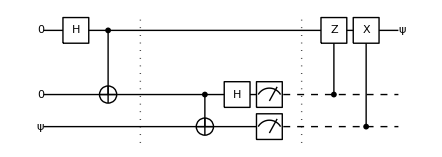

```mathematica
in=ProductState[S[3]->c@{0,1},"Label"->Ket[ψ]];
out=ProductState[S[1]->c@{0,1},"Label"->Ket[ψ]];qc=QuantumCircuit[in,Ket[S@{1,2}],S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",CNOT[S[2],S[3]],S[2,6],{Measurement[S[2,3]],Measurement[S[3,3]]},"Separator",ControlledGate[S[2],S[1,3]],ControlledGate[S[3],S[1,1]],
out,"Invisible"->S[1.5]]
```

It consists of three stages separated by the vertical dashed lines in the quantum circuit. The first stage is to share the entangled pair of qubits. The second in the middle corresponds to the Bell measurement. The final stage transmits the measurement outcomes to Alice, and Alice adjusts the state of her qubit according to the classical information.

Rearrange the quantum circuit elements to reinterpret the quantum teleportation protocol in stabilizer formalism.

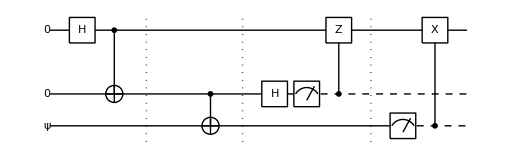

```mathematica
qc1=QuantumCircuit[in,Ket[S@{1,2}],S[1,6],CNOT[S[1],S[2]],"Separator","Spacer"];
qc2=QuantumCircuit[qc1,CNOT[S[2],S[3]],"Separator"];
qc3=QuantumCircuit[qc2,S[2,6],Measurement[S[2,3]],ControlledGate[S[2],S[1,3]],"Separator"];
qc4=QuantumCircuit[qc3,Measurement[S[3,3]],ControlledGate[S[3],S[1,1]],"Invisible"->S[1.5]]
```

At the point marked by the first vertical line, the relevant stabilizer 𝒮 is generated by

```mathematica
G1=S[1,1]**S[2,1];
G2=S[1,3]**S[2,3];
PauliForm[{G1,G2},S@{1,2,3}]
```

{X⊗X⊗I,Z⊗Z⊗I}

```mathematica
G1**qc1==qc1//Elaborate
G2**qc1==qc1//Elaborate
```

True

True

We pick up two logical Pauli operators

```mathematica
LX=S[3,1];
LZ=S[3,3];
PauliForm[{LX,LZ},S@{1,2,3}]
```

{I⊗I⊗X,I⊗I⊗Z}

One can convince oneself that these logical Pauli operators commute with all the generators (and hence all elements) of the stabilizer.

```mathematica
Flatten@Outer[Commutator,{LX,LZ},{G1,G2}]
```

{0,0,0,0}

Under the CNOT gate from qubit B (for Bob) to C (for Charlie), that is, at the point marked by the second vertical line, the generators and the logical Pauli operators are transformed to

```mathematica
op=CNOT[S[2],S[3]];
G1=op**G1**Dagger[op];
G2=op**G2**Dagger[op];
PauliForm[{G1,G2},S@{1,2,3}]
LX=op**LX**Dagger[op]//Elaborate;
LZ=op**LZ**Dagger[op]//Elaborate;
PauliForm[{LX,LZ},S@{1,2,3}]
```

{X⊗X⊗X,Z⊗Z⊗I}

{I⊗I⊗X,I⊗Z⊗Z}

Next, we measure observable X on qubit B, M=I⊗X⊗I. Note that M anti-commutes with the second generator G_2 while it commutes with G_1.

```mathematica
M=S[2,1];PauliForm[M,S@{1,2,3}]
G=G2;
```

I⊗X⊗I

```mathematica
Commutator[M,G1]
Anticommutator[M,G2]
```

0

0

We thus have to apply G_2 conditioned on the measurement outcome. We update G_2 by replacing it with M.

```mathematica
G1=S[1,1]**S[2,1]**S[3,1];
G2=M;
PauliForm[{G1,G2},S@{1,2,3}]
```

{X⊗X⊗X,I⊗X⊗I}

Note also that M anti-commutes with the logical Pauli operator Z̄ whereas it commutes with X̄. We need to replace logical Pauli operator Z̄ by G_2 Z̄.

```mathematica
LX=LX;
LZ=G**LZ;
PauliForm[{LX,LZ},S@{1,2,3}]
```

{I⊗I⊗X,Z⊗I⊗Z}

At this stage, it is safe to drop qubit B off since its state does not change nor is used after the measurement outcome has been recorded.

Finally, we measure the observable Z on qubit C, M=I⊗I⊗Z. We note that M anti-commutes with generator G_1 and logical Pauli operator X̄.

```mathematica
M=S[3,3];PauliForm[M,S@{1,2,3}]
G=G1;
```

I⊗I⊗Z

In accordance with the same prescription as above, we apply G_1 conditioned on the measurement outcome, and the generators and the logical Pauli operators are updated as follows

```mathematica
G1=M;
G2=G2;
LX=G**LX;
LZ=LZ;
PauliForm[{G1,G2},S@{1,2,3}]
PauliForm[{LX,LZ},S@{1,2,3}]
```

{I⊗I⊗Z,I⊗X⊗I}

{X⊗X⊗I,Z⊗I⊗Z}

A quantum circuit that more closely follows the above transformations would look like the following.

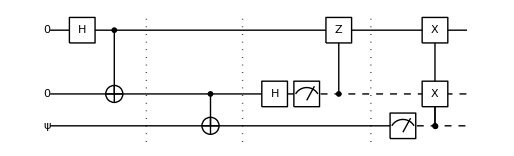

```mathematica
new=QuantumCircuit[in,Ket[S@{1,2}],S[1,6],CNOT[S[1],S[2]],"Separator","Spacer",CNOT[S[2],S[3]],"Separator",S[2,6],Measurement[S[2,3]],ControlledGate[S[2],S[1,3]],"Separator",Measurement[S[3,3]],{ControlledGate[S[3],S[1,1]],ControlledGate[S[3],S[2,1]]},"Invisible"->S[1.5]]
```

However, the operation Xon the second qubit is meaningless since the qubit was already measured. Therefore, the quantum circuit is equivalent to the standard one for quantum teleportation.

To confirm it, we test the result by performing the quantum circuit model many times.

```mathematica
out=Table[ExpressionFor[qc4],{6}]/.c[0]*Conjugate[c[0]]+c[1]*Conjugate[c[1]]->1;
KetFactor[#,S@{2,3}]&/@out//TableForm
```

0_S_21_S_3⊗(1/2 (c_0 0_S_1+c_1 1_S_1))
0_S_20_S_3⊗(1/2 (c_0 0_S_1+c_1 1_S_1))
1_S_20_S_3⊗(1/2 (c_0 0_S_1+c_1 1_S_1))
0_S_20_S_3⊗(1/2 (c_0 0_S_1+c_1 1_S_1))
0_S_20_S_3⊗(1/2 (c_0 0_S_1+c_1 1_S_1))
1_S_20_S_3⊗(1/2 (c_0 0_S_1+c_1 1_S_1))

Each time, the final state on the first qubit is the same regardless of the outcome of the measurements on the second and third qubit.

### Remote Implementation of CNOT

The second example is a remote implementation of the CNOT gate using the pre-shared entangled pair of qubits.

Suppose that Alice and Bob are located far away from each other, and there is no quantum channel available between them. Fortunately, they had shared and are maintaining a maximally entangled pair of qubits, and there is a classical channel available for communication between them.

Alice wants to implement a CNOT gate targeted on Bob's qubit, not the one involved in the shared entangled pair, controlled by her own qubit. The protocol is summarized in the following quantum circuit.

```mathematica
Let[Integer,x,m];
in=KetRegulate[Ket[S[1]->x[1],S[4]->x[4]],S@{1,2,3,4}];
out=Ket[S[1]->x[1],S@{2,3}->m@{2,3},S[4]->Mod[x[1]+x[4],2]];
core=QuantumCircuit[S[2,6],CNOT[S[2],S[3]],"Separator","Spacer",
{CNOT[S[1],S[2]],CNOT[S[3],S[4]]},
Measurement[S[2,3]],CNOT[S[2],S@{3,4}],
S[3,6],Measurement[S[3,3]],ControlledGate[S[3],S[1,3]]];
```

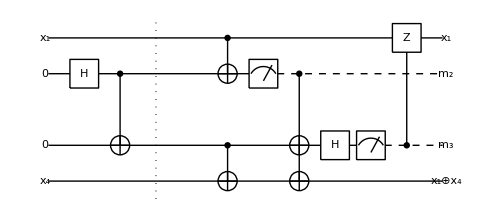

```mathematica
qc=QuantumCircuit[in,core,out,"PortSize"->{0.65,2},"Invisible"->S[2.5]]
```

The initial stage marked by the vertical dashed line is just to share an entangled pair, and we start the analysis from this point. Then, the generators of the stabilizer are given by

```mathematica
G1=S[2,1]**S[3,1];
G2=S[2,3]**S[3,3];
PauliForm[{G1,G2},ss=S@{1,2,3,4}]//TableForm
```

I⊗X⊗X⊗I
I⊗Z⊗Z⊗I

We also pick four logical Pauli operators to describe two logical qubits, one on Alice’s side (A) and the other on Bob’s side (B).

```mathematica
Xa=S[1,1];
Za=S[1,3];
Xb=S[4,1];
Zb=S[4,3];
PauliForm[{Xa,Za,Xb,Zb},ss]//TableForm
```

X⊗I⊗I⊗I
Z⊗I⊗I⊗I
I⊗I⊗I⊗X
I⊗I⊗I⊗Z

The two subsequent CNOT gates transform the generators as

```mathematica
op=CNOT[S[1],S[2]]**CNOT[S[3],S[4]];
G1=op**G1**Dagger[op];
G2=op**G2**Dagger[op];
PauliForm[{G1,G2},ss]//TableForm
```

I⊗X⊗X⊗X
Z⊗Z⊗Z⊗I

and the logical Pauli operators

```mathematica
Xa=op**Xa**Dagger[op]//Elaborate;
Za=op**Za**Dagger[op]//Elaborate;
Xb=op**Xb**Dagger[op]//Elaborate;
Zb=op**Zb**Dagger[op]//Elaborate;
PauliForm[{Xa,Za,Xb,Zb},ss]//TableForm
```

X⊗X⊗I⊗I
Z⊗I⊗I⊗I
I⊗I⊗I⊗X
I⊗I⊗Z⊗Z

Next we measure Z on the second qubit, M=I⊗Z⊗I⊗I. M anti-commutes with G_1 and (X̄)_a. Therefore, we apply G_1 conditioned on the measurement outcome, and update the generators and logical Pauli operators as follows.

```mathematica
M=S[2,3];
G=G1;
```

```mathematica
G1=M;
G2=G2;
PauliForm[{G1,G2},ss]//TableForm
```

I⊗Z⊗I⊗I
Z⊗Z⊗Z⊗I

Finally, we measure X on the third qubit, M=I⊗I⊗X⊗I. M anti-commutes with G_2 and (Z̄)_b. We apply G_2 conditioned on the measurement outcome. The generators and logical Pauli operators are transformed as follows

```mathematica
M=S[3,1];
G=G2;
```

```mathematica
G1=G1;
G2=M;
PauliForm[{G1,G2},ss]//TableForm
```

I⊗Z⊗I⊗I
I⊗I⊗X⊗I

```mathematica
Xa=Xa;
Za=Za;
Xb=Xb;
Zb=G**Zb;
PauliForm[{Xa,Za,Xb,Zb},ss]//TableForm
```

X⊗X⊗I⊗I
Z⊗I⊗I⊗I
I⊗I⊗I⊗X
Z⊗Z⊗I⊗Z

At this stage, the generators are meaningless since the second and third qubits are now classical after the two measurements. If one followed the above steps of analysis faithfully, she would get a quantum circuit of the form

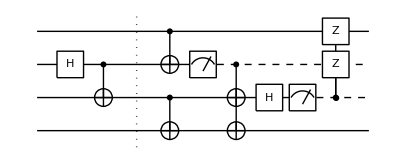

```mathematica
QuantumCircuit[
S[2,6],CNOT[S[2],S[3]],"Separator",
{CNOT[S[1],S[2]],CNOT[S[3],S[4]]},
Measurement[S[2,3]],CNOT[S[2],S@{3,4}],
S[3,6],Measurement[S[3,3]],{ControlledGate[S[3],S[1,3]],ControlledGate[S[3],S[2,3]]}
]
```

However, the classically-conditioned operation of X on the third qubit right before the measurement of X does not affect the result. On the other hand, the classically-conditioned operation of Z on the second qubit is meaningless because the qubit has already been measured.

Check whether the quantum circuit works as expected.

```mathematica
bs=Basis[S@{1,4}];
new=core**bs;
Thread[bs->new]//TableForm
```

0_S_10_S_4→0_S_10_S_21_S_30_S_4
0_S_11_S_4→0_S_11_S_20_S_31_S_4
1_S_10_S_4→1_S_11_S_20_S_31_S_4
1_S_11_S_4→1_S_10_S_21_S_30_S_4

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪The Pauli and Clifford Groups
▪Stabilizer Codes
▪Quantum Error-Correction Codes
▪Quantum Information Systems with Q3

| Related Links
▪D. Gottesman, Physical Review A 54, 1862 (1996)https://doi.org/10.1103%2Fphysreva.54.1862, “Class of quantum error- correcting codes saturating the quantum Hamming bound.”
▪R. Cleve and D. Gottesman, Physical Review A 56, 76 (1997)https://doi.org/10.1103/physreva.56.76, "Efficient computations of encodings for quantum error correction."
▪D. Gottesman (1997)https://arxiv.org/abs/quant-ph/9705052, Stabilizer Codes and Quantum Error Correction (Ph.D. Thesis, California Institute of Technology, 1997).
▪D. Gottesman, Physical Review A 57, 127 (1998)https://doi.org/10.1103/PhysRevA.57.127, “Theory of fault-tolerant quantum computation.”
▪D. Gottesman (1999)http://arxiv.org/abs/quant-ph/9807006, “The Heisenberg Representation of Quantum Computers,” in Proceedings of XXII International Colloquium on Group Theoretical Methods in Physics, edited by S. P. Corney, R. Delbourgo, and P. D. Jarvis (International Press, Cambridge, MA, 1999).
▪S. Aaronson and D. Gottesman, Physical Review A 70, 052328 (2004)https://doi.org/10.1103/physreva.70.052328, “Improved simulation of stabilizer circuits.”
▪D. Browne and H. Briegel (2016)https://doi.org/10.1002/9783527805785.ch21, "One-Way Quantum Computation," in Quantum Information: From Foundation to Quantum Technology Applications, edited by D. Bruß and G. Leuchs (Wiley, 2016).
▪D. M. Greenberger, M. A. Horne, and A. Zeilinger (1989)https://arxiv.org/abs/0712.0921, "Going beyond Bell’s theorem,” in Bell’s Theorem, Quantum Theory, and Conceptions of the Universe, edited by M. Kafatos (Kluwer Academic, Dordrecht, The Netherlands, 1989).
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).